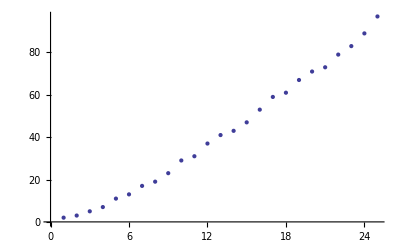

```mathematica
ListPlot[Prime[Range[25]]]
```

```mathematica
0
```

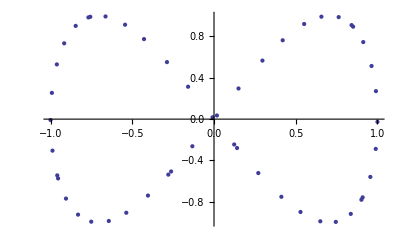

```mathematica
ListPlot[Table[{Sin[n],Sin[2n]},{n,50}]]
```

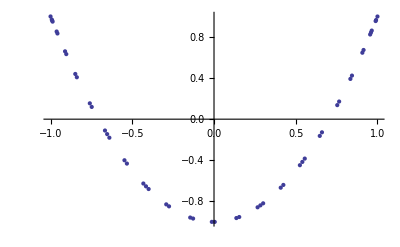

```mathematica
ListPlot[Table[{Cos[n],Cos[2n]},{n,50}]]
```

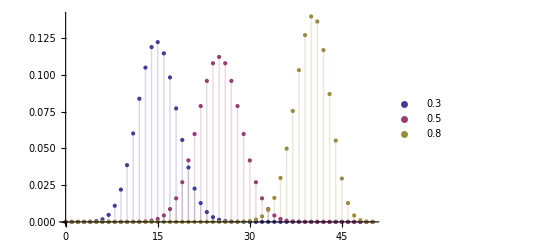

```mathematica
ListPlot[Table[{k,
PDF[BinomialDistribution[50,p],k]},{p,{0.3,0.5,0.8}},{k,0,50}],
Filling->Axis, PlotLegends->{0.3,0.5,0.8}]
```

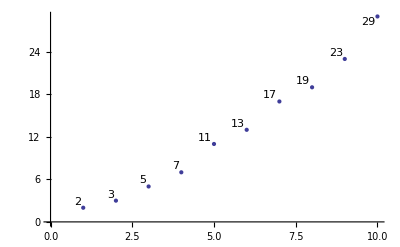

```mathematica
ListPlot[Labeled[#,#]&/@ Table[Prime[n],{n,10}],
PlotStyle->PointSize[Medium]]
```

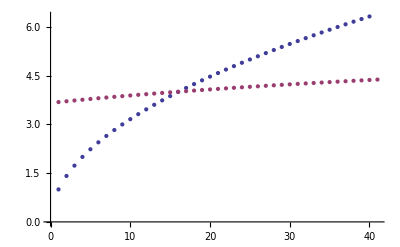

```mathematica
ListPlot[{Labeled[Sqrt[Range[40]],"sqrt"],Labeled[Log[Range[40,80]],"log"]}]
```

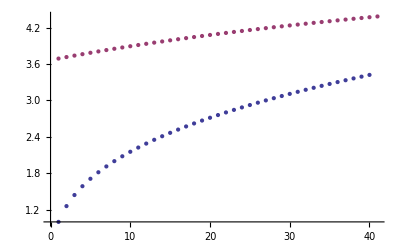

```mathematica
ListPlot[{Labeled[CubeRoot[Range[40]],"cuberoot"],Labeled[Log[Range[40,80]],"log"]}]
```

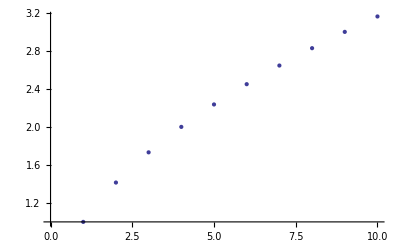

```mathematica
ListPlot[Quantity[Sqrt[Range[10]],"Meters"]]
```

```mathematica
data= Last[
Reap[NIntegrate[Sin[x]^2,{x,0,2Pi},
EvaluationMonitor->Sow[{x,Sin[x]^2}]]]];
ListPlot[data]
```

-Graphics-

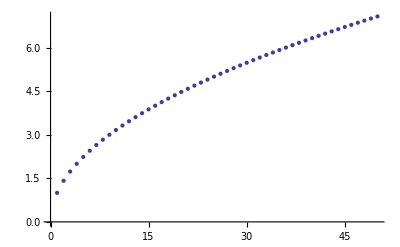

```mathematica
ListPlot[Quantity[Sqrt[Range[50]],"meters"]]
```

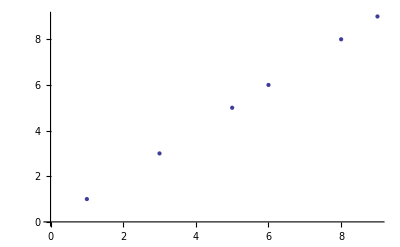

```mathematica
ListPlot[{1,1+i,3,None,5,6,Missing["NotAvilable"],8,9}]
```

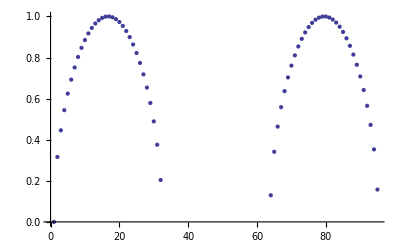

```mathematica
ListPlot[Sqrt[Sin[Range[0,3Pi,0.1]]]]
```

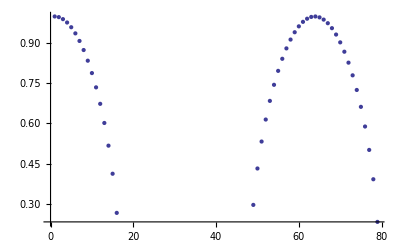

```mathematica
ListPlot[Sqrt[Cos[Range[0,3Pi,0.1]]]]
```

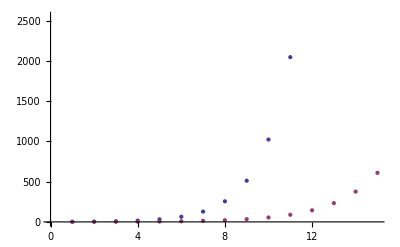
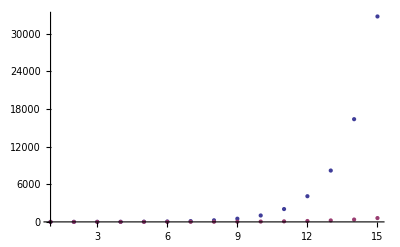

```mathematica
{ListPlot[{2^Range[15],Fibonacci[Range[15]]}],
ListPlot[{2^Range[15],Fibonacci[Range[15]]},PlotRange->All]}
```

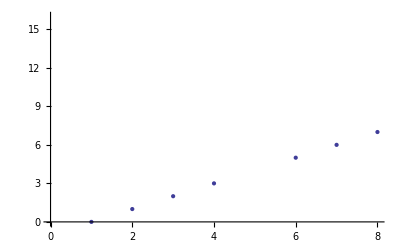
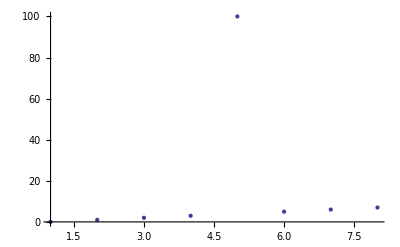

```mathematica
{ListPlot[{0,1,2,3,100,5,6,7}],ListPlot[{0,1,2,3,100,5,6,7},PlotRange->All]}
```

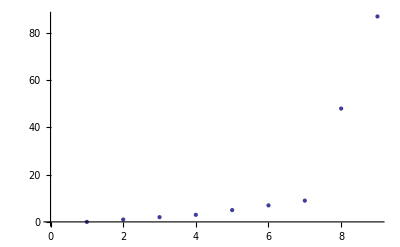
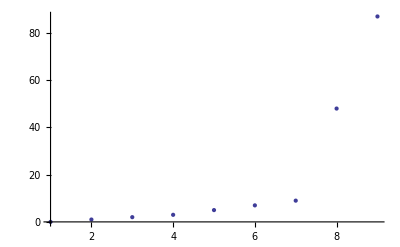

```mathematica
{ListPlot[{0,1,2,3,5,7,9,48,87}],ListPlot[{0,1,2,3,5,7,9,48,87},PlotRange->All]}
```